```mathematica
NotebookFileName[]
```

/home/rediax/Documents/Projects/Cellular Automata India/tmp2.nb

```mathematica
r23=Subscript[#,2,3]&/@Range[0,255];
```

```mathematica
evos[rules_,space_]:=Module[{conect,inits},
ParallelTable[
inits=IntegerDigits[#,2,space]&/@Range[0,2^space-1];
conect=Map[
CaArray[rules[[i]],#,1][[1]]->CaArray[rules[[i]],#,1][[2]]&,
inits];
rules[[i]]->Graph[conect],
{i,1,Length[rules]}]
]
```

```mathematica
TransMap[Subscript[n_,2,3],space_]:=Module[{tbl,configs,idx},tbl=IntegerDigits[n,2,8];(*tabla:vecindad 7,6,...,0*)configs=IntegerDigits[Range[0,2^space-1],2,space];
idx=4 (RotateRight/@configs)+2 configs+(RotateLeft/@configs);
(*sucesor de la config i (como entero,1-indexado)*)Map[FromDigits[#,2]&,Map[tbl[[8-#]]&,idx,{2}]]+1]
```

```mathematica
TransMap[Subscript[30,2,3],2]
```

{1,2,3,1}

```mathematica
CanonFuncGraph[f_List]:=Module[{n=Length[f],indeg,preds,code,queue,visited,cycles},indeg=ConstantArray[0,n];
Do[indeg[[f[[i]]]]++,{i,n}];
preds=ConstantArray[{},n];
code=ConstantArray[Null,n];
(*codificación canónica de los árboles,pelando hojas*)queue=Flatten@Position[indeg,0];
While[queue=!={},With[{v=First[queue]},queue=Rest[queue];
code[[v]]={Sort[preds[[v]]]};
With[{w=f[[v]]},AppendTo[preds[[w]],code[[v]]];
If[--indeg[[w]]==0,AppendTo[queue,w]]]]];
(*los nodos con indeg>0 restante están en ciclos*)visited=ConstantArray[False,n];cycles={};
Do[If[indeg[[v]]>0&&!visited[[v]],Module[{c={},w=v},While[!visited[[w]],visited[[w]]=True;
AppendTo[c,w];w=f[[w]]];
AppendTo[cycles,c]]],{v,n}];
(*llave:por ciclo,rotación lexicográficamente mínima de los códigos*)Sort[Module[{seq=({Sort[preds[[#]]]}&/@#)},First@Sort@Table[RotateLeft[seq,j],{j,Length[seq]}]]&/@cycles]]
```

```mathematica
r23f=ParallelMap[TransMap[#,13]&,r23];
gr23=Values@GroupBy[Transpose[{r23,r23f}],CanonFuncGraph@*Last->First];
```

```mathematica
Iconize[gr23]
```

```mathematica
gr23s13=;
gr23s12=;
gr23s6=;
wkr23=;
```

```mathematica
fusions=Select[Table[{g,Select[wkr23,SubsetQ[g,#]&]},{g,gr23s6}],Length[#[[2]]]>1&]
fusions=Select[Table[{g,Select[wkr23,SubsetQ[g,#]&]},{g,gr23s12}],Length[#[[2]]]>1&]
fusions=Select[Table[{g,Select[wkr23,SubsetQ[g,#]&]},{g,gr23s13}],Length[#[[2]]]>1&]
```

Vemos que las reglas de herencia incluso demuestra que 2 reglas si son iguales, porque, si hacemos el fusions con gr23s13 vemos que el ultimo elemento, que combina uno de 2 y uno de 4 en realidad muestra que 2 reglas si estan heredando. Ahora lo que nos interesa saber es, que medaida de similitud podemos usar para comparar los grafos. ya vimos que esta medida nos dice si pertenecen al mismo

```mathematica
clases23=gr23s13;
```

```mathematica
clases=gr23s4;                     (*tu lista de clases*)
reps=First/@clases;         (*un representante por clase*)

perfiles=Table[PerfilPT[TransMap[r,n]],{n,3,10},{r,reps}];
Dtotal=Mean@Table[Outer[DistanciaPT[#1,#2,j+2]&,perfiles[[j]],perfiles[[j]],1],{j,1,8}];

Similitud=Exp[-5 Dtotal];
```

```mathematica
Similitud[[1,3]]
reps[[{1,3}]]
```

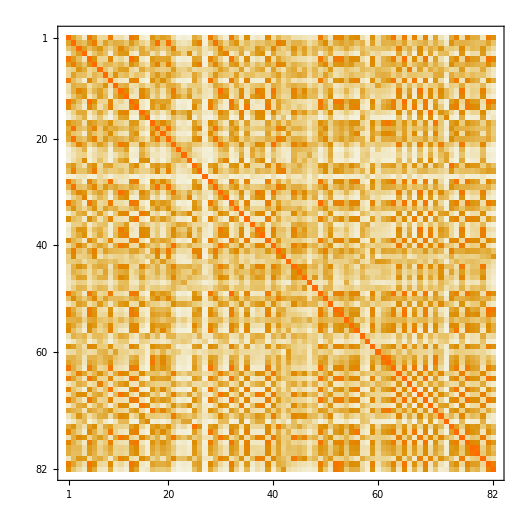

```mathematica
MatrixPlot[Similitud]
```

```mathematica
Similitud[[1,256]]
Similitud[[256,1]]
```

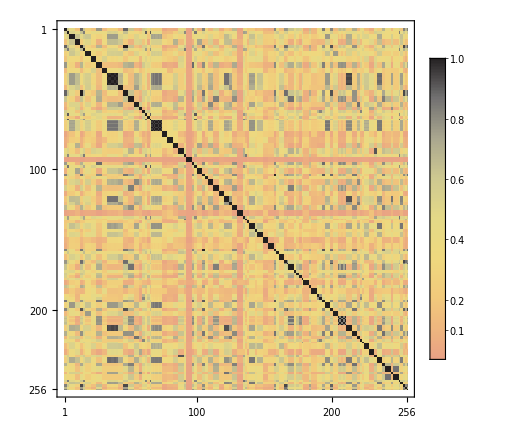

```mathematica
MatrixPlot[Similitud,ColorFunction->"CMYKColors",PlotLegends->Automatic]
```

```mathematica
PerfilPT[f_List]:=Module[{n=Length[f],indeg,per,trans,queue,qi,v,w,c},indeg=ConstantArray[0,n];Do[indeg[[f[[i]]]]++,{i,n}];
per=ConstantArray[0,n];trans=ConstantArray[-1,n];
(*ciclos:período y transitorio 0*)Module[{visited=ConstantArray[False,n],resto=indeg},(*pela hojas para marcar árboles*)
queue=Flatten@Position[resto,0];qi=1;
While[qi<=Length[queue],v=queue[[qi++]];w=f[[v]];
If[--resto[[w]]==0,AppendTo[queue,w]]];
Do[If[resto[[v]]>0&&!visited[[v]],c={};w=v;
While[!visited[[w]],visited[[w]]=True;AppendTo[c,w];w=f[[w]]];
(per[[#]]=Length[c];trans[[#]]=0)&/@c],{v,n}]];
(*transitorios:propaga hacia atrás desde los ciclos*)Module[{pend=Flatten@Position[trans,-1]},While[pend=!={},pend=Select[pend,If[trans[[f[[#]]]]>=0,trans[[#]]=trans[[f[[#]]]]+1;per[[#]]=per[[f[[#]]]];False,True]&]]];
{Sort[N@Log2[per]],Sort[N@Log2[trans+1]]}]

DistanciaPT[{pa_,ta_},{pb_,tb_},nn_]:=(Mean[Abs[pa-pb]]+Mean[Abs[ta-tb]])/nn

(*pipeline completo*)
perfiles=Table[PerfilPT[TransMap[r,n]],{n,1,8},{r,r23}];
Dtotal=Mean@Table[Outer[DistanciaPT[#1,#2,n]&,perfiles[[n]],perfiles[[n]],1],{n,1,8}];
Similitud=Exp[-5 Dtotal];   (*λ=5,ajustable*)
```